# HyperBloch package tutorial

## Hatano-Nelson model

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Hatano-Nelson model tutorial on the HyperCells&HyperBloch website.  In this tutorial, we will see how non-Hermitian hyperbolic lattice models can be set up through the construction of nearest-neighbor tight-binding models on the {6,4}-lattice with (supercell) model graphs (constructed through HyperBloch’s sister package HyperCells). Specifically, we will consider Hermiticity-breaking terms, such as gains and losses, and a variant of the Hatano-Nelson.

## Preliminaries:

### Remarks:

Before using the notebook to the Hatano-Nelson model tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc
{6,4}-tess-NN_T2.2_3.hcm
{6,4}-tess-NN_T2.2_3_sc-T5.4.hcs
{6,4}-tess-NN_T2.2_3_sc-T9.3.hcs

In case no such files exist in your current directory, please follow the instructions in the  HyperBloch Hatano-Nelson model tutorial, or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Needed functions:

In previous tutorials, such as getting started with the HyperBloch package and HyperBloch Supercells tutorial etc., we have calculated the density of states of various tight-binding models via exact diagonalization and random samples. We predefine a function in order to calculate the eigenvalues for the (non-reciprocal) Abelian Bloch Hamiltonians that we will construct. We  take advantage of the independence of different momentum sectors and parallelize the computation, where we partition the set of Npts into  Nruns subunits:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## (Supercell) model graphs:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

where we consider the unit cell T2.2 as the primitive cell.

### Import (supercell) model graphs:

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NN_T2.2_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{6,4}-tess-NN_T2.2_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst= Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Visualize model graph:

We can visualize the model graph with the high-level visualization function VisualizeModelGraph:

```mathematica
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
NumberOfGenerations->3,
Elements-><|
	ShowCellGraphFlattened->{},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->300]
```

-Graphics-

## Complex staggered on-site potential

### Construct Hamiltonians:

#### On-site terms:

In order to construct the non-Hermitian Abelian Bloch Hamiltonian with a complex staggered on-site potential, we need to identify the sub-lattices. The needed information can be extracted by printing the vertex list of the model graph:

```mathematica
VertexList@pcmodel["Graph"]
```

{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6}}

Comparing the list of vertices with the model representation we have previously visualized, we can assign the staggered on-site potential  ±(M+ⅈ η) as follows:

```mathematica
mVec =(M+ⅈ η){1,-1,-1,1,1,-1}; 
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### Hamiltonians:

The non-Hermitian Abelian Bloch Hamiltonians with complex on-site potentials can be constructed through the AbelianBlochHamiltonian function:

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,onsitePC,-1&,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,onsitePC,-1&,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{M->0.1,η->1}, 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize real and imaginary part of the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

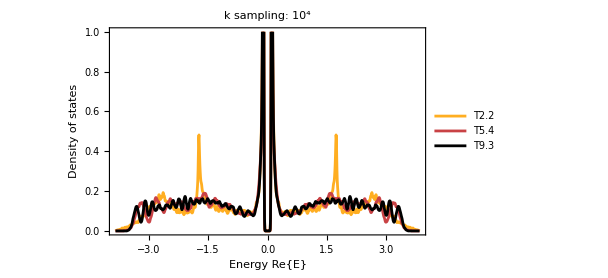
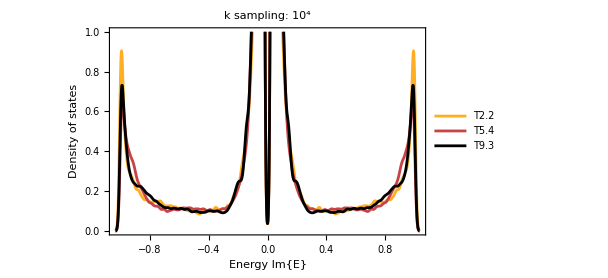

```mathematica
Row[
{SmoothHistogram[Re@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Re{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,1},PlotStyle->cLst],

SmoothHistogram[Im@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Im{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,1},PlotStyle->cLst]}
]
```

### Complex energy spectrum:

The complex spectrum can be visualized by using the built-in function ComplexListPlot of Mathematica. However, this might take a few minutes to be displayed. As such let us thin down our data sets by taking smaller subsets through random samples:

```mathematica
ComplexRandomThinning[evs_,Npts_]:=Module[{keys},
keys=Keys[evs];
Association[
Table[key->RandomSample[Flatten[evs[key]],Npts],
{key,keys}]]]
```

We choose to visualize the complex spectrum for a randomly chosen subset of 10^3 data points:

```mathematica
ComplexListPlot[ComplexRandomThinning[evals,1000],
AspectRatio->1/1.5,Frame->{{True,True},{True,True}},
FrameLabel->{{"Im{E}",None},{"Re{E}",None}},
FrameStyle->Directive[Black,30],ImageSize->500,
LabelStyle->20,PlotMarkers->{"●",Scaled[0.015]},
PlotRange->{{-4,4},{-1.1,1.1}},PlotStyle->cLst]
```

-Graphics-

## {6,4} Hatano-Nelson model:

### Visualize the Hatano-Nelson model:

A possible  variant of the Hatano-Nelson model for the {6,4}-lattice consists of (weakly) coupled 1 dimensional chains with asymmetric hopping amplitudes and zero on-site potential.

Assigning  the  appropriate  hopping  amplitudes  relies  on  the  identification  of  the  set  of  directed  edges  connecting  vertices  in  the  model  graph  of  the  primitive  cell. The needed information can be extracted by printing the edge list of the model graph:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{{1,1},1,7}},{2,3}{2,1}{1,{{1,2},6,12}},{2,1}{2,3}{1,{{1,3},13,23}},{2,2}{2,4}{1,{{1,4},2,8}},{2,4}{2,2}{1,{{1,5},15,19}},{2,2}{2,1}{1,{{1,6},14,24}},{2,5}{2,3}{1,{{1,7},5,11}},{2,3}{2,5}{1,{{1,8},18,22}},{2,4}{2,6}{1,{{1,9},3,9}},{2,6}{2,4}{1,{{1,10},16,20}},{2,6}{2,5}{1,{{1,11},4,10}},{2,5}{2,6}{1,{{1,12},17,21}}}

We can make use of the option EdgeFilter of the function ShowCellGraphFlattened within the function VisualizeModelGraph in order to visualize the one
dimensional chains we want to endow with asymmetric hopping amplitudes. To do so, we choose to asymmetrically couple the vertices {{2,1},{2,2}}, {{2,3},{2,5}} and {{2,4},{2,6}} by first defining the list:

```mathematica
edgesInChains={
{2,1}->{2,2},{2,2}->{2,1},
{2,3}->{2,5},{2,5}->{2,3} ,
{2,4}->{2,6},{2,6}->{2,4}};
```

The graph representation of the Hatano-Nelson with decoupled one dimensional chains on the primitive cell looks as follows:

```mathematica
HNgraph=VisualizeModelGraph[pcmodel,
Elements-><|
ShowCellGraphFlattened->{
EdgeFilter->( MemberQ[edgesInChains,#[[{1,2}]]]&)},
ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
CellGraph->pcell,
NumberOfGenerations->3,
ImageSize->300]
```

-Graphics-

#### Show equivalent inter-cell edges:

It is instructive to also visualize the equivalent (translated) inter-cell edges starting outside the cell and ending inside.
First, let us extract the inter-cell edges. Each inter-cell edge is associated with a non-trivial translation:

```mathematica
pcmodel["EdgeTranslations"]
```

{1,1,g1,1,g3,g2,1,g4^-1*g2^-1,1,g4,1,g3^-1*g1^-1}

In addition, we restrict the list to the edges present in the Hatano-Nelson chains specified in our previously defined list:

```mathematica
intercedges = Select[Transpose[{EdgeList@pcmodel["Graph"], pcmodel["EdgeTranslations"]}],MemberQ[edgesInChains,#[[1, {1,2}]]]&&#[[2]]!="1"&][[;;,1]];
```

We can use the function  GetCellGraphEdge and its option ShowEquivalentEdge in order visualize specific edges and equivalent (translated) inter-cell edges in the Poincaré disk:

```mathematica
Show[HNgraph,
Graphics[{AbsoluteThickness[2],
GetCellGraphEdge[pcmodel,#, ShowEquivalentEdge->True]/.Line->Arrow}]&/@intercedges
]
```

-Graphics-

The visualization enables us to ensure we construct the corresponding Abelian Bloch Hamiltonian consistently.

### Constructing Hamiltonians:

#### Symmetric and asymmetric NN-hopping amplitudes:

The hopping amplitudes can be assigned by inspecting the list of edges in the model graph, however, we may as well choose to proceed programmatically by filtering through the list.

We define a vector which we will use to assign asymmetric hopping amplitudes to the one dimensional chains:

```mathematica
hoppingVecHatanoNelson= If[MemberQ[edgesInChains,#[[{1,2}]]],1,0]&/@EdgeList[pcmodel["Graph"]];
```

In addition, we define another vector which we will use to (weakly) couple the Hatano-Nelson chains by symmetric hopping amplitudes:

```mathematica
hoppingVecPerturbation=If[MemberQ[edgesInChains,#[[{1,2}]]],0,1]&/@EdgeList[pcmodel["Graph"]];
```

Canonical direction:

The hopping amplitudes in the canonical direction can be assigned as follows:

```mathematica
hoppingVecCanonical = (t+γ)hoppingVecHatanoNelson + δ hoppingVecPerturbation;
```

```mathematica
hoppingsPCCanonical=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVecCanonical];
```

Opposite to the canonical direction:

Similarly, the hopping amplitudes opposite to the canonical direction can be assigned as follows:

```mathematica
hoppingVecOpposite = (t-γ)hoppingVecHatanoNelson + δ hoppingVecPerturbation;
```

```mathematica
hoppingsPCOpposite=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVecOpposite];
```

#### Hamiltonians:

The non-reciprocal Abelian Bloch Hamiltonians for the primitive cell and supercells can be constructed through the NonReciprocalAbelianBlochHamiltonian function:

Primitive cell:

```mathematica
Hpc=NonReciprocalAbelianBlochHamiltonian[pcmodel,1,0&,hoppingsPCCanonical,hoppingsPCOpposite,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->NonReciprocalAbelianBlochHamiltonian[scmodels[#],1,0&,hoppingsPCCanonical,hoppingsPCOpposite,PCModel->pcmodel,CompileFunction->True]
&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{t->0.5,γ->0.5,δ->0.1}, 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize real and imaginary part of the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

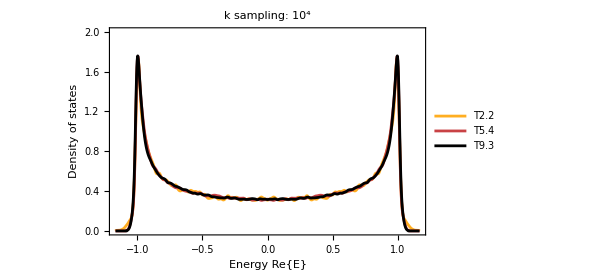
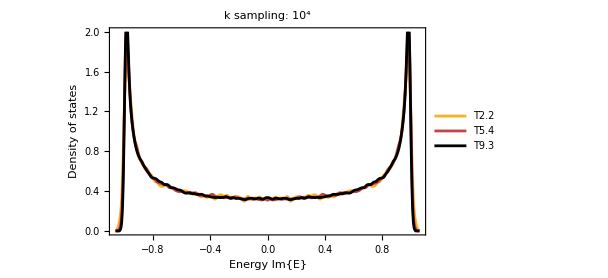

```mathematica
Row[
{SmoothHistogram[Re@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Re{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,1},PlotStyle->cLst],

SmoothHistogram[Im@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Im{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,1},PlotStyle->cLst]}
]
```

### Complex energy spectrum:

We choose to visualize the complex spectrum for a randomly chosen subset of 10^3 data points using the previously defined thinning function:

```mathematica
ComplexListPlot[ComplexRandomThinning[evals,1000],
AspectRatio->1/1.5,Frame->{{True,True},{True,True}},
FrameLabel->{{"Im{E}",None},{"Re{E}",None}},
FrameStyle->Directive[Black,30],ImageSize->500,
LabelStyle->20,PlotMarkers->{"●",Scaled[0.015]},
PlotRange->{{-2,2},{-2,2}},PlotStyle->cLst]
```

-Graphics-

## {6,4} Hatano-Nelson model with gains and losses (bonus):

Let us combine both models in order to introduce a line gap and two point gaps.

### Constructing Hamiltonians:

#### Hamiltonians:

The corresponding non-reciprocal Abelian Bloch Hamiltonians can be constructed as follows:

Primitive cell:

```mathematica
Hpc=NonReciprocalAbelianBlochHamiltonian[pcmodel,1,onsitePC,hoppingsPCCanonical,hoppingsPCOpposite,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->NonReciprocalAbelianBlochHamiltonian[scmodels[#],1,onsitePC,hoppingsPCCanonical,hoppingsPCOpposite,PCModel->pcmodel,CompileFunction->True]
&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{t->0.5,γ->0.5,δ->0.1, M->1,η->1}, 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize real and imaginary part of the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

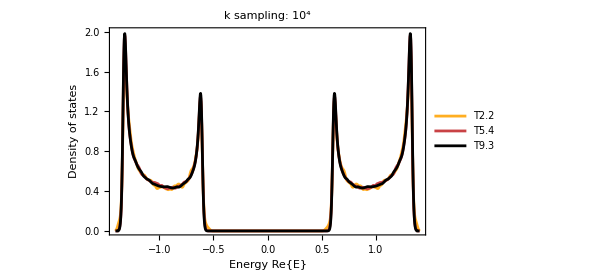
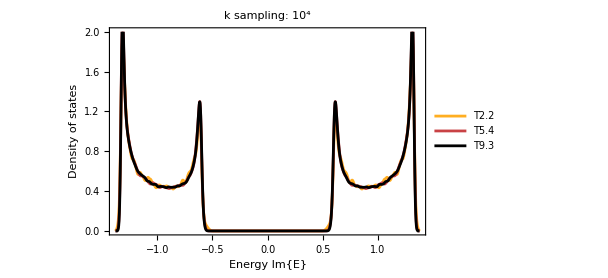

```mathematica
Row[
{SmoothHistogram[Re@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Re{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,2},PlotStyle->cLst],

SmoothHistogram[Im@evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy Im{E}","Density of states"},
FrameStyle->Black,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
ImageSize->450,LabelStyle->20,PlotLabel->"k sampling: 10^4",
PlotRange->{0,2},PlotStyle->cLst]}
]
```

### Complex energy spectrum:

We choose to visualize the complex spectrum for a randomly chosen subset of 10^3 data points using the previously defined thinning function:

```mathematica
ComplexListPlot[ComplexRandomThinning[evals,1000],
AspectRatio->1/1.5,Frame->{{True,True},{True,True}},
FrameLabel->{{"Im{E}",None},{"Re{E}",None}},
FrameStyle->Directive[Black,30],ImageSize->500,
LabelStyle->20,PlotMarkers->{"●",Scaled[0.015]},
PlotRange->{{-2,2},{-2,2}},PlotStyle->cLst]
```

-Graphics-

```mathematica
NotebookSave[]
```